# Homogeneous 2nd order linear differential equation

```mathematica
ClearAll["Global`*"];
```

## Homogeneous 2nd order linear differential equation with constant coefficients and initial conditions

```mathematica
equation=y''[t]-1.5y'[t]+5y[t]==0;
```

```mathematica
initialCondition={y'[0]==0,y[0]==1};
```

```mathematica
sol=First@DSolve[{equation,initialCondition},y[t],t];
```

{y[t]→1. ⅇ^(0.75 t) Cos[2.10654 t]-0.356034 ⅇ^(0.75 t) Sin[2.10654 t]}

```mathematica
y=y[t]/.sol
```

1. ⅇ^(0.75 t) Cos[2.10654 t]-0.356034 ⅇ^(0.75 t) Sin[2.10654 t]

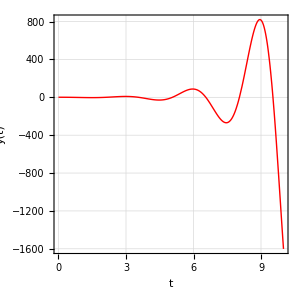

```mathematica
Plot[y,{t,0,10},
FrameLabel->{{"y(t)",None},{"t","Solution"}},
Frame->True,
GridLines->Automatic,
GridLinesStyle->Automatic,
RotateLabel->True,
PlotRange->All,
AspectRatio->1,
PlotStyle->{Thick,Red}]
```